```mathematica
If[ $FrontEnd === Null,
		$FeynCalcStartupMessages = False;
		Print["Computation of the matrix element squared for the q_i qbar_i -> g g scattering in QCD at tree level"];
];
If[$Notebooks === False, $FeynCalcStartupMessages = False];
$LoadFeynArts= True;
$FAVerbose = 0;
Global`$LoadAddOns={"FeynHelpers"};
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

$FAVerbose::shdw: Symbol $FAVerbose appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

FeynHelpers 1.1.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
instree = InsertFields[CreateTopologies[0, 2 -> 2,ExcludeTopologies->{Tadpoles}], {V[1],V[5]}-> {F[3, {1}], -F[3, {1}]},
		InsertionLevel -> {Classes},Model -> "SMQCD", ExcludeParticles -> {S[1], S[2],S[3], V[1],V[2],V[3],V[4],U[5]}];
(*Paint[instree, ColumnsXRows -> {2, 1}, Numbering->Simple,SheetHeader->None,ImageSize->{768,256}];*)
```

loading generic model file /Users/bwwang/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/bwwang/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/SMQCD.mod

loading classes model file /Users/bwwang/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 10 Classes, and 10 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

Restoring 0 Generic, 10 Classes, and 10 Particles fields

in total: 2 Classes insertions

```mathematica
FCGV["MU"]=0

FCGV["EL"]=e
```

0

e

> Top. 1: 1 diagram

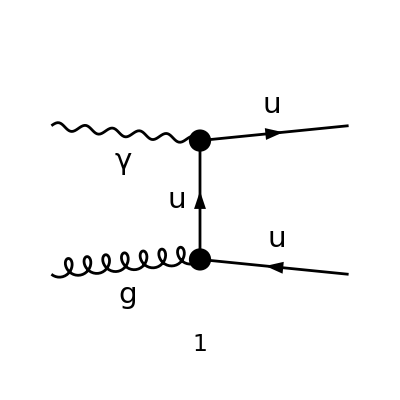

```mathematica
ins=DiagramExtract[instree,1];
Paint[ins, ColumnsXRows -> {2, 1}, Numbering->Simple,SheetHeader->None,ImageSize->{768,256}];
```

```mathematica
amp=FCFAConvert[CreateFeynAmp[ins,Truncated -> False],IncomingMomenta->{p1,p2},OutgoingMomenta->{q1,q2},(*LoopMomenta->{k},*)
DropSumOver->True,ChangeDimension->D,UndoChiralSplittings->True,List->False,SMP->False]/.Pair[LorentzIndex[Lor_, D], Momentum[Polarization[p1, I], D]]->FVD[p1,Lor](*/.SMP["m_u"]->0*)//ChangeDimension[#,D]&//Contract
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

(2 e g_s T_Col3Col4^Glu2 (φ(q1)).(γ·p1).(γ·(p2-q2)).(γ·ε(p2)).(φ(-q2)))/(3 (q2-p2)^2)

```mathematica
ClearScalarProducts
```

```mathematica
SetMandelstam[s,t,u,p1,p2,-q1,-q2,I*Q,0,0,0];
```

```mathematica
?SetMandelstam
```

SetMandelstam[s, t, u, p1, p2, p3, p4, m1, m2, m3, m4] defines the Mandelstam variables  s=(p1+p2)^2, t=(p1+p3)^2, u=(p1+p4)^2 and sets the pi on-shell: p1^2=m1^2, p2^2=m2^2, p3^2=m3^2, p4^2=m4^2. Note that p1 +  p2 + p3 + p4 = 0 is assumed.



SetMandelstam[x, {p1, p2, p3, p4, p5}, {m1, m2, m3, m4, m5}] defines x[i, j] = (pi+pj)^2 and sets the pi on-shell. The pi satisfy: p1 + p2 + p3 + p4 + p5 = 0.

```mathematica
SqAmp=(1/8)(amp*
		(ComplexConjugate[amp]//FCRenameDummyIndices))//FeynAmpDenominatorSplit//PropagatorDenominatorExplicit//
		SUNSimplify[#,Explicit->True,SUNNToCACF->False]&//FermionSpinSum[#, ExtraFactor -> 1/2^2]&//
		(*Contract//*)ReplaceAll[#,{DiracTrace->Tr,SUNN->3}]&(*//DoPolarizationSums[#,p1,0]&*)//
		DoPolarizationSums[#,p2,0]&//Contract//Simplify(*//FortranForm*)
```

((D-2) e^2 g_s^2 (Q^4+Q^2 (s+t+u)+s t))/(9 t)

```mathematica
SqAmp/.u->-s-t-Q^2
```

((D-2) e^2 g_s^2 (Q^4+Q^2 (s+t+u)+s t))/(9 t)